### Definitions

```mathematica
Φ[x_]:=CDF[NormalDistribution[0,1],x]
```

```mathematica
dp[S_,τ_,K_,r_,δ_,σ_]:=1/(σ √τ)*(Log[S/K]+(r-δ+σ^2/2)*τ)
dm[S_,τ_,K_,r_,δ_,σ_]:=1/(σ √τ)*(Log[S/K]+(r-δ-σ^2/2)*τ)
```

```mathematica
BSCall[S_,t_,K_,T_,r_,δ_,σ_]:=S*Exp[-δ*(T-t)]*Φ[dp[S,T-t,K,r,δ,σ]]-K*Exp[-r*(T-t)]*Φ[dm[S,T-t,K,r,δ,σ]]
BSPut[S_,t_,K_,T_,r_,δ_,σ_]:=-S*Exp[-δ*(T-t)]*Φ[-dp[S,T-t,K,r,δ,σ]]+K*Exp[-r*(T-t)]*Φ[-dm[S,T-t,K,r,δ,σ]]
```

### Solving for the maximal c

#### Definition of the objective function

```mathematica
g[x_]:=Exp[-3 r](1+α)+x/S0 BSCall[S0,0,S0(1+α/x),3,r,δ,σ]
```

#### Numerical implementation

```mathematica
r=0.07;
δ=0.02;
α=0.02;
S0=1;
```

```mathematica
x[σ_]:=O/.FindRoot[Exp[-3 r](1+α)+O/S0 BSCall[S0,0,S0(1+α/O),3,r,δ,σ]==1,{O,0.9}]
Dx[σ_]:=(x[σ]^2 Derivative[0,0,0,0,0,0,1][BSCall][S0,0,S0+(S0 α)/x[σ],3,r,δ,σ])/(-BSCall[S0,0,S0+(S0 α)/x[σ],3,r,δ,σ] x[σ]+S0 α Derivative[0,0,1,0,0,0,0][BSCall][S0,0,S0+(S0 α)/x[σ],3,r,δ,σ])
```

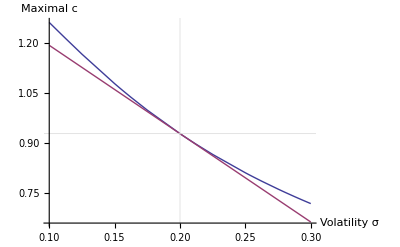

```mathematica
Plot[{x[u],x[0.2]+(u-0.2)*Dx[0.2]},{u,0.1,0.3},PlotPoints->2,GridLines->{{0.2},{x[0.2]}},AxesLabel->{"Volatility σ","Maximal c"}]
```

```mathematica
{x[u],x[0.2]+(u-0.2)*Dx[0.2]}/.u->0.18//Quiet
{x[u],x[0.2]+(u-0.2)*Dx[0.2]}/.u->0.22//Quiet
```

{0.983107,0.980401}

{0.877197,0.874658}

#### Question e)

```mathematica
g[0.8]/.σ->0.2
```

0.9749

```mathematica
g[0.8]/.σ->0.35
```

1.04353